```mathematica
Clear[equs]
```

```mathematica
G=1.;m1=1;m2=1;m3=1;
```

```mathematica
equs={x1''[t]==-(G  m2 (x1[t]-x2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(G  m3 (x1[t]-x3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)),y1''[t]==-(G  m2 (y1[t]-y2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(G m3 (y1[t]-y3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)),x2''[t]==-(G  m1 (-x1[t]+x2[t]))/(((-x1[t]+x2[t])^2+(-y1[t]+y2[t])^2)^(3/2))-(G m3  (x2[t]-x3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),y2''[t]==-(G  m1(-y1[t]+y2[t]))/(((-x1[t]+x2[t])^2+(-y1[t]+y2[t])^2)^(3/2))-(G  m3(y2[t]-y3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),x3''[t]==-(G m1(-x1[t]+x3[t]))/(((-x1[t]+x3[t])^2+(-y1[t]+y3[t])^2)^(3/2))-(G  m2(-x2[t]+x3[t]))/(((-x2[t]+x3[t])^2+(-y2[t]+y3[t])^2)^(3/2)),y3''[t]==-(G m1(-y1[t]+y3[t]))/(((-x1[t]+x3[t])^2+(-y1[t]+y3[t])^2)^(3/2))-(G  m2(-y2[t]+y3[t]))/(((-x2[t]+x3[t])^2+(-y2[t]+y3[t])^2)^(3/2)),x1[0]==-1,x1'[0]==0.306893,x2[0]==0,x2'[0]==-2  0.306893,x3[0]==1,x3'[0]==0.306893,y1[0]==0,y1'[0]==0.125507,y2[0]==0,y2'[0]==-2  0.125507,y3[0]==0,y3'[0]==0.125507};
```

```mathematica
sol=NDSolve[equs,{x1,x2,x3,y1,y2,y3},{t,0,7}];
```

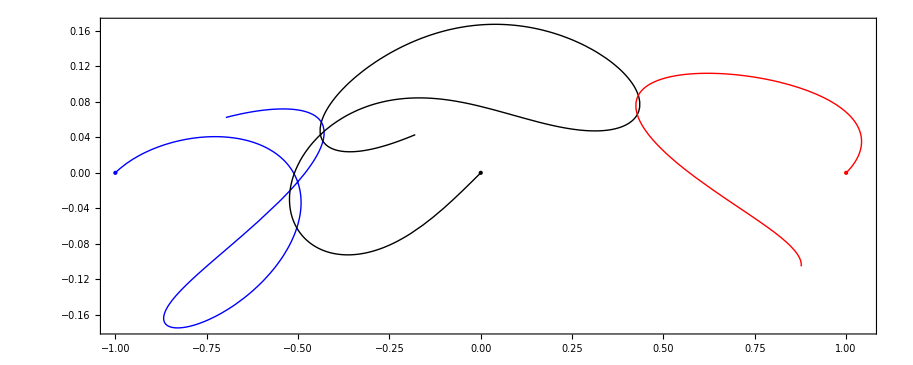

```mathematica
Show[ParametricPlot[Evaluate[Flatten[{x1[t],y1[t]}/.sol,1]],{t,0,2},Axes->False,PlotStyle->{Thick,Blue}],ParametricPlot[Evaluate[Flatten[{x2[t],y2[t]}/.sol,1]],{t,0,2},Axes->False,PlotStyle->{Thick,Black}],ParametricPlot[Evaluate[Flatten[{x3[t],y3[t]}/.sol,1]],{t,0,2},Axes->False,PlotStyle->{Thick,Red}],Graphics[{PointSize[Large],Black,Point[{0,0}],Blue,Point[{-1,0}],Red,Point[{1,0}]}],PlotRange->All,AspectRatio->Automatic,Frame->True]
```

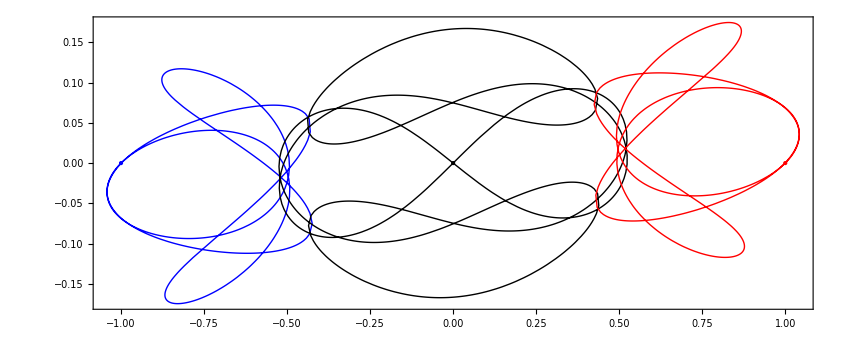

```mathematica
Show[ParametricPlot[Evaluate[Flatten[{x1[t],y1[t]}/.sol,1]],{t,0,6.24},Axes->False,PlotStyle->{Thick,Blue}],ParametricPlot[Evaluate[Flatten[{x2[t],y2[t]}/.sol,1]],{t,0,6.24},Axes->False,PlotStyle->{Thick,Black}],ParametricPlot[Evaluate[Flatten[{x3[t],y3[t]}/.sol,1]],{t,0,6.24},Axes->False,PlotStyle->{Thick,Red}],Graphics[{PointSize[Large],Black,Point[{0,0}],Blue,Point[{-1,0}],Red,Point[{1,0}]}],PlotRange->All,AspectRatio->Automatic,Frame->True]
```